## Analysis of the in-patch model

#### This document includes:

The in-patch model and its solutions

Code to generate Figures 1B-1E

## Solutions for one strain

Solve for the chelation rate

```mathematica
a=kf;
b=-(kf (sFe + ϵ α M [t]+ sApo) + dr^2);
c=kf sFe ( ϵ α M[t] + sApo);
Qstar = (-b - Sqrt[b^2-4 a c])/(2 a)
```

(dr^2+kf (sApo+sFe+α ϵ M[t])-√(-4 kf^2 sFe (sApo+α ϵ M[t])+(-dr^2-kf (sApo+sFe+α ϵ M[t]))^2))/(2 kf)

```mathematica
eq = 0==((1-α)γ vh Qstar/ (vh M[t] + Kh dr) -dm )M[t]
```

0==M[t] (-dm+(vh (1-α) γ (dr^2+kf (sApo+sFe+α ϵ M[t])-√(-4 kf^2 sFe (sApo+α ϵ M[t])+(-dr^2-kf (sApo+sFe+α ϵ M[t]))^2)))/(2 kf (dr Kh+vh M[t])))

```mathematica
sols=Solve[eq, M[t],NonNegativeReals,Assumptions->Flatten[{0<=α<=1,sApo>=0,Map[#>0&,{vh,γ,Kh,ϵ,dr, dm,sFe,kf}]}]]
```

{{M[t]→ConditionalExpression[0, ]},{M[t]→ConditionalExpression[1/(2 dm kf vh (dm-α γ ϵ+α^2 γ ϵ))(-2 dm^2 dr kf Kh+dm dr^2 vh γ+dm kf sApo vh γ+dm kf sFe vh γ-dm dr^2 vh α γ-dm kf sApo vh α γ-dm kf sFe vh α γ+dm dr kf Kh α γ ϵ-dm dr kf Kh α^2 γ ϵ-kf sFe vh α γ^2 ϵ+2 kf sFe vh α^2 γ^2 ϵ-kf sFe vh α^3 γ^2 ϵ)-1/(2 dm kf vh Abs[dm-α γ ϵ+α^2 γ ϵ])(√(dm^2 dr^4 vh^2 γ^2+2 dm^2 dr^2 kf sApo vh^2 γ^2+dm^2 kf^2 sApo^2 vh^2 γ^2+2 dm^2 dr^2 kf sFe vh^2 γ^2-2 dm^2 kf^2 sApo sFe vh^2 γ^2+dm^2 kf^2 sFe^2 vh^2 γ^2-2 dm^2 dr^4 vh^2 α γ^2-4 dm^2 dr^2 kf sApo vh^2 α γ^2-2 dm^2 kf^2 sApo^2 vh^2 α γ^2-4 dm^2 dr^2 kf sFe vh^2 α γ^2+4 dm^2 kf^2 sApo sFe vh^2 α γ^2-2 dm^2 kf^2 sFe^2 vh^2 α γ^2+dm^2 dr^4 vh^2 α^2 γ^2+2 dm^2 dr^2 kf sApo vh^2 α^2 γ^2+dm^2 kf^2 sApo^2 vh^2 α^2 γ^2+2 dm^2 dr^2 kf sFe vh^2 α^2 γ^2-2 dm^2 kf^2 sApo sFe vh^2 α^2 γ^2+dm^2 kf^2 sFe^2 vh^2 α^2 γ^2-2 dm^2 dr^3 kf Kh vh α γ^2 ϵ-2 dm^2 dr kf^2 Kh sApo vh α γ^2 ϵ+2 dm^2 dr kf^2 Kh sFe vh α γ^2 ϵ+4 dm^2 dr^3 kf Kh vh α^2 γ^2 ϵ+4 dm^2 dr kf^2 Kh sApo vh α^2 γ^2 ϵ-4 dm^2 dr kf^2 Kh sFe vh α^2 γ^2 ϵ-2 dm^2 dr^3 kf Kh vh α^3 γ^2 ϵ-2 dm^2 dr kf^2 Kh sApo vh α^3 γ^2 ϵ+2 dm^2 dr kf^2 Kh sFe vh α^3 γ^2 ϵ-2 dm dr^2 kf sFe vh^2 α γ^3 ϵ+2 dm kf^2 sApo sFe vh^2 α γ^3 ϵ-2 dm kf^2 sFe^2 vh^2 α γ^3 ϵ+6 dm dr^2 kf sFe vh^2 α^2 γ^3 ϵ-6 dm kf^2 sApo sFe vh^2 α^2 γ^3 ϵ+6 dm kf^2 sFe^2 vh^2 α^2 γ^3 ϵ-6 dm dr^2 kf sFe vh^2 α^3 γ^3 ϵ+6 dm kf^2 sApo sFe vh^2 α^3 γ^3 ϵ-6 dm kf^2 sFe^2 vh^2 α^3 γ^3 ϵ+2 dm dr^2 kf sFe vh^2 α^4 γ^3 ϵ-2 dm kf^2 sApo sFe vh^2 α^4 γ^3 ϵ+2 dm kf^2 sFe^2 vh^2 α^4 γ^3 ϵ+dm^2 dr^2 kf^2 Kh^2 α^2 γ^2 ϵ^2-2 dm^2 dr^2 kf^2 Kh^2 α^3 γ^2 ϵ^2+dm^2 dr^2 kf^2 Kh^2 α^4 γ^2 ϵ^2-2 dm dr kf^2 Kh sFe vh α^2 γ^3 ϵ^2+6 dm dr kf^2 Kh sFe vh α^3 γ^3 ϵ^2-6 dm dr kf^2 Kh sFe vh α^4 γ^3 ϵ^2+2 dm dr kf^2 Kh sFe vh α^5 γ^3 ϵ^2+kf^2 sFe^2 vh^2 α^2 γ^4 ϵ^2-4 kf^2 sFe^2 vh^2 α^3 γ^4 ϵ^2+6 kf^2 sFe^2 vh^2 α^4 γ^4 ϵ^2-4 kf^2 sFe^2 vh^2 α^5 γ^4 ϵ^2+kf^2 sFe^2 vh^2 α^6 γ^4 ϵ^2)), ]},{M[t]→ConditionalExpression[1/(2 dm kf vh (dm-α γ ϵ+α^2 γ ϵ))(-2 dm^2 dr kf Kh+dm dr^2 vh γ+dm kf sApo vh γ+dm kf sFe vh γ-dm dr^2 vh α γ-dm kf sApo vh α γ-dm kf sFe vh α γ+dm dr kf Kh α γ ϵ-dm dr kf Kh α^2 γ ϵ-kf sFe vh α γ^2 ϵ+2 kf sFe vh α^2 γ^2 ϵ-kf sFe vh α^3 γ^2 ϵ)+1/(2 dm kf vh Abs[dm-α γ ϵ+α^2 γ ϵ])(√(dm^2 dr^4 vh^2 γ^2+2 dm^2 dr^2 kf sApo vh^2 γ^2+dm^2 kf^2 sApo^2 vh^2 γ^2+2 dm^2 dr^2 kf sFe vh^2 γ^2-2 dm^2 kf^2 sApo sFe vh^2 γ^2+dm^2 kf^2 sFe^2 vh^2 γ^2-2 dm^2 dr^4 vh^2 α γ^2-4 dm^2 dr^2 kf sApo vh^2 α γ^2-2 dm^2 kf^2 sApo^2 vh^2 α γ^2-4 dm^2 dr^2 kf sFe vh^2 α γ^2+4 dm^2 kf^2 sApo sFe vh^2 α γ^2-2 dm^2 kf^2 sFe^2 vh^2 α γ^2+dm^2 dr^4 vh^2 α^2 γ^2+2 dm^2 dr^2 kf sApo vh^2 α^2 γ^2+dm^2 kf^2 sApo^2 vh^2 α^2 γ^2+2 dm^2 dr^2 kf sFe vh^2 α^2 γ^2-2 dm^2 kf^2 sApo sFe vh^2 α^2 γ^2+dm^2 kf^2 sFe^2 vh^2 α^2 γ^2-2 dm^2 dr^3 kf Kh vh α γ^2 ϵ-2 dm^2 dr kf^2 Kh sApo vh α γ^2 ϵ+2 dm^2 dr kf^2 Kh sFe vh α γ^2 ϵ+4 dm^2 dr^3 kf Kh vh α^2 γ^2 ϵ+4 dm^2 dr kf^2 Kh sApo vh α^2 γ^2 ϵ-4 dm^2 dr kf^2 Kh sFe vh α^2 γ^2 ϵ-2 dm^2 dr^3 kf Kh vh α^3 γ^2 ϵ-2 dm^2 dr kf^2 Kh sApo vh α^3 γ^2 ϵ+2 dm^2 dr kf^2 Kh sFe vh α^3 γ^2 ϵ-2 dm dr^2 kf sFe vh^2 α γ^3 ϵ+2 dm kf^2 sApo sFe vh^2 α γ^3 ϵ-2 dm kf^2 sFe^2 vh^2 α γ^3 ϵ+6 dm dr^2 kf sFe vh^2 α^2 γ^3 ϵ-6 dm kf^2 sApo sFe vh^2 α^2 γ^3 ϵ+6 dm kf^2 sFe^2 vh^2 α^2 γ^3 ϵ-6 dm dr^2 kf sFe vh^2 α^3 γ^3 ϵ+6 dm kf^2 sApo sFe vh^2 α^3 γ^3 ϵ-6 dm kf^2 sFe^2 vh^2 α^3 γ^3 ϵ+2 dm dr^2 kf sFe vh^2 α^4 γ^3 ϵ-2 dm kf^2 sApo sFe vh^2 α^4 γ^3 ϵ+2 dm kf^2 sFe^2 vh^2 α^4 γ^3 ϵ+dm^2 dr^2 kf^2 Kh^2 α^2 γ^2 ϵ^2-2 dm^2 dr^2 kf^2 Kh^2 α^3 γ^2 ϵ^2+dm^2 dr^2 kf^2 Kh^2 α^4 γ^2 ϵ^2-2 dm dr kf^2 Kh sFe vh α^2 γ^3 ϵ^2+6 dm dr kf^2 Kh sFe vh α^3 γ^3 ϵ^2-6 dm dr kf^2 Kh sFe vh α^4 γ^3 ϵ^2+2 dm dr kf^2 Kh sFe vh α^5 γ^3 ϵ^2+kf^2 sFe^2 vh^2 α^2 γ^4 ϵ^2-4 kf^2 sFe^2 vh^2 α^3 γ^4 ϵ^2+6 kf^2 sFe^2 vh^2 α^4 γ^4 ϵ^2-4 kf^2 sFe^2 vh^2 α^5 γ^4 ϵ^2+kf^2 sFe^2 vh^2 α^6 γ^4 ϵ^2)), ]}}

```mathematica
allSols=Solve[eq, M[t]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{M[t]→0},{M[t]→1/(2 dm vh^2 (dm-α γ ϵ+α^2 γ ϵ))(-vh (2 dm^2 dr Kh-(dm dr^2 vh γ)/kf-dm sApo vh γ-dm sFe vh γ+(dm dr^2 vh α γ)/kf+dm sApo vh α γ+dm sFe vh α γ-dm dr Kh α γ ϵ+dm dr Kh α^2 γ ϵ+sFe vh α γ^2 ϵ-2 sFe vh α^2 γ^2 ϵ+sFe vh α^3 γ^2 ϵ)-√(-4 dm vh^2 (dm^2 dr^2 Kh^2-(dm dr^3 Kh vh γ)/kf-dm dr Kh sApo vh γ-dm dr Kh sFe vh γ+(dm dr^3 Kh vh α γ)/kf+dm dr Kh sApo vh α γ+dm dr Kh sFe vh α γ+sApo sFe vh^2 γ^2-2 sApo sFe vh^2 α γ^2+sApo sFe vh^2 α^2 γ^2) (dm-α γ ϵ+α^2 γ ϵ)+vh^2 (2 dm^2 dr Kh-(dm dr^2 vh γ)/kf-dm sApo vh γ-dm sFe vh γ+(dm dr^2 vh α γ)/kf+dm sApo vh α γ+dm sFe vh α γ-dm dr Kh α γ ϵ+dm dr Kh α^2 γ ϵ+sFe vh α γ^2 ϵ-2 sFe vh α^2 γ^2 ϵ+sFe vh α^3 γ^2 ϵ)^2))},{M[t]→1/(2 dm vh^2 (dm-α γ ϵ+α^2 γ ϵ))(-vh (2 dm^2 dr Kh-(dm dr^2 vh γ)/kf-dm sApo vh γ-dm sFe vh γ+(dm dr^2 vh α γ)/kf+dm sApo vh α γ+dm sFe vh α γ-dm dr Kh α γ ϵ+dm dr Kh α^2 γ ϵ+sFe vh α γ^2 ϵ-2 sFe vh α^2 γ^2 ϵ+sFe vh α^3 γ^2 ϵ)+√(-4 dm vh^2 (dm^2 dr^2 Kh^2-(dm dr^3 Kh vh γ)/kf-dm dr Kh sApo vh γ-dm dr Kh sFe vh γ+(dm dr^3 Kh vh α γ)/kf+dm dr Kh sApo vh α γ+dm dr Kh sFe vh α γ+sApo sFe vh^2 γ^2-2 sApo sFe vh^2 α γ^2+sApo sFe vh^2 α^2 γ^2) (dm-α γ ϵ+α^2 γ ϵ)+vh^2 (2 dm^2 dr Kh-(dm dr^2 vh γ)/kf-dm sApo vh γ-dm sFe vh γ+(dm dr^2 vh α γ)/kf+dm sApo vh α γ+dm sFe vh α γ-dm dr Kh α γ ϵ+dm dr Kh α^2 γ ϵ+sFe vh α γ^2 ϵ-2 sFe vh α^2 γ^2 ϵ+sFe vh α^3 γ^2 ϵ)^2))}}

### Extinction equilibrium

With no biomass, Q* depends on sApo

```mathematica
QstarExtinct =Qstar/.M[t]->0
```

(dr^2+kf (sApo+sFe)-√(-4 kf^2 sApo sFe+(-dr^2-kf (sApo+sFe))^2))/(2 kf)

Per capita growth is

```mathematica
RareGrowth = ((1-α) γ vh QstarExtinct)/(Kh dr)-dm
```

-dm+((dr^2+kf (sApo+sFe)-√(-4 kf^2 sApo sFe+(-dr^2-kf (sApo+sFe))^2)) vh (1-α) γ)/(2 dr kf Kh)

To invade, alpha must be below this critical value:

```mathematica
alphacrit=FullSimplify[SolveValues[RareGrowth==0,α][[1]]]
```

1-(dm dr Kh (dr^2+kf (sApo+sFe)+√(dr^4+kf^2 (sApo-sFe)^2+2 dr^2 kf (sApo+sFe))))/(2 kf sApo sFe vh γ)

### No siderophore investment

0==M[t] (-dm+((dr^2+kf (sApo+sFe)-√(-4 kf^2 sApo sFe+(-dr^2-kf (sApo+sFe))^2)) vh γ)/(2 kf (dr Kh+vh M[t])))

```mathematica
Mzero=FullSimplify[SolveValues[eq/.α->0,M[t]]][[2]]
```

-(dr Kh)/vh+((dr^2+kf (sApo+sFe)-√(dr^4+kf^2 (sApo-sFe)^2+2 dr^2 kf (sApo+sFe))) γ)/(2 dm kf)

## Numeric solution

```mathematica
Clear[defaults];
defaults={
sFe->5,
sApo->1,
dr->1,
dm->0.1,

kf->1,
γ->3,
vh->10,Kh->1,
ϵ->1.
};
```

```mathematica
Mzero/.defaults
```

24.1225

```mathematica
Off[Greater::nord] (* Complains when comparing real and imaginary numbers, but doesn't matter *)
```

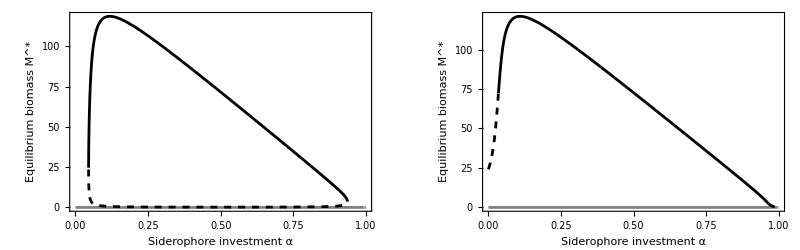

```mathematica
GraphicsRow[{
Plot[Evaluate[M[t]/.(sols/.{sApo->0,vh->1}/.defaults)],{α,0,1},
Frame->True,FrameLabel->{"Siderophore investment α","Equilibrium biomass M^*"},
PlotTheme->"Default",BaseStyle->Directive[FontSize->13,FontColor->Black],
PlotStyle->{Gray,{Black,Dashed},Black},
LabelStyle->Directive[FontSize->11,FontColor->Black]
],
Plot[Evaluate[M[t]/.(sols/.defaults)],{α,0,1},
Frame->True,FrameLabel->{"Siderophore investment α","Equilibrium biomass M^*"},
PlotTheme->"Default",BaseStyle->Directive[FontSize->13,FontColor->Black],
PlotStyle->{Gray,{Black,Dashed},Black},
LabelStyle->Directive[FontSize->11,FontColor->Black]
]
}]
```

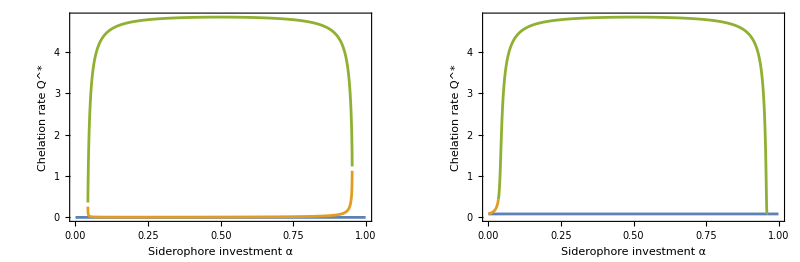

```mathematica
GraphicsRow[{
Plot[Evaluate[Qstar/.sApo->0/.defaults/.(sols/.sApo->0/.defaults)],{α,0,1},
Frame->True,FrameLabel->{"Siderophore investment α","Chelation rate Q^*"},
PlotTheme->"Default",BaseStyle->Directive[FontSize->13,FontColor->Black],
LabelStyle->Directive[FontSize->11,FontColor->Black]
],
Plot[Evaluate[Qstar/.sApo->0.1/.defaults/.(sols/.sApo->0.1/.defaults)],{α,0,1},
Frame->True,FrameLabel->{"Siderophore investment α","Chelation rate Q^*"},
PlotTheme->"Default",BaseStyle->Directive[FontSize->13,FontColor->Black],
LabelStyle->Directive[FontSize->11,FontColor->Black]
]
}]
```

#### For our parameters, R_holo* << Kh

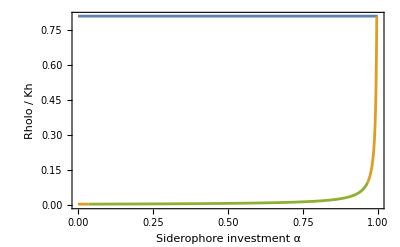

```mathematica
Plot[Evaluate[(Qstar/(vh/Kh M[t] + dr))/Kh/. defaults /. sols/.defaults],{α,0,1},
Frame->True,FrameLabel->{"Siderophore investment α","Rholo / Kh"},
PlotTheme->"Default",BaseStyle->Directive[FontSize->13,FontColor->Black],LabelStyle->Directive[FontSize->11,FontColor->Black]
]
```

#### Saddle node bifurcation in s_apo and alpha

```mathematica
implicitRate=eq[[2]]/M[t]; 

ContourPlot3D[Evaluate[implicitRate/. {M[t]->m,sApo->sapo,γ->1}/. defaults]==0,{α,0,0.4},{sapo,0,0.04},{m,0.01,40},Contours->{0},Mesh->None,ContourStyle->Directive[Orange,Opacity[0.8]],BoundaryStyle->Black,AxesLabel->{"α","s_apo","M*"}]
```

-Graphics3D-

```mathematica
M[t]/.(allSols/.α->0/.defaults)
```

{0,24.1225,185.677}

### Value of α that maximizes biomass (α̂)

```mathematica
M[t]/.(allSols/.α->0.5/.defaults)
```

{0,72.6598,-2.35981}

```mathematica
maximize=NMaximize[{M[t]/.(allSols/.defaults)[[2]], 0.05<=α<=0.4}, α]
```

{121.012,{α→0.109202}}

```mathematica
alphahat=α/.maximize[[2]]
```

0.109202

```mathematica
maxbiomass=maximize[[1]]
```

121.012

### Biomass for zero investment

```mathematica
Mzero/.defaults
```

24.1225

### Bifurcation diagram

```mathematica
alphahat
```

0.109202

```mathematica
crit=alphacrit/.defaults
```

0.995872

```mathematica
lines=Evaluate[M[t]/.(sols/.defaults)];
lines/.α->0.01
lines/.α->0.1
```

Greater::nord: Invalid comparison with 3.37018+1.34544 ⅈ attempted.

{0,30.9406,Undefined}

Greater::nord: Invalid comparison with 0.370755+0.147983 ⅈ attempted.

{0,Undefined,120.845}

```mathematica
plotlines={
(* Zero stability changes at the critical point *)
ConditionalExpression[lines[[1]],α<crit],
ConditionalExpression[lines[[1]],α>crit],
(* Split at alpha_hat for the pareto front *)
ConditionalExpression[lines[[2]],α<alphahat],
ConditionalExpression[lines[[2]],α>alphahat],
ConditionalExpression[lines[[3]],α<alphahat],
ConditionalExpression[lines[[3]],α>alphahat]
};
```

```mathematica
plotlines/.α->0.05
```

{0,Undefined,Undefined,Undefined,101.866,Undefined}

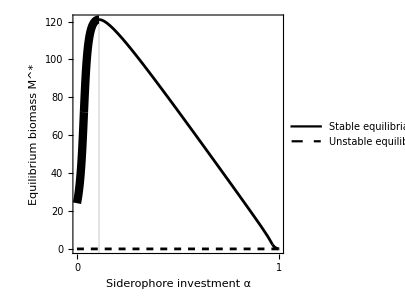

```mathematica
pltvsalpha=Plot[plotlines,{α,0,1},
PlotStyle->{{Black,Dashed},Black,{Black,Thickness[0.02]},Black, {Black,Thickness[0.02]},Black},
Frame->True,FrameLabel->{"Siderophore investment α","Equilibrium biomass M^*"},
PlotTheme->"Default",BaseStyle->Directive[FontSize->13,FontColor->Black],LabelStyle->Directive[FontSize->11,FontColor->Black],
PlotLegends->Placed[LineLegend[{Black,{Black,Dashed}},{"Stable equilibria", "Unstable equilibrium"},LegendMarkerSize->{22,10}],{Right,Top}],
PlotRange->{-4,All},
PlotRangeClipping->False,
FrameTicks->{{Automatic,None},{{0,1},None}},
Prolog->{
Directive[LightGray],
Line[{{alphahat,-4},{alphahat,maxbiomass}}],
Black,FontSize->11,
Text["α̂",{alphahat,-8.5}]
},
ImageSize->300,AspectRatio->1
]
```

### Bifurcation diagram, no s_apo

```mathematica
lines=Evaluate[M[t]/.(sols/.{sApo->0,dm->0.3}/.defaults)];
lines/.α->0.01
lines/.α->0.1
```

{0,Undefined,Undefined}

{0,Undefined,Undefined}

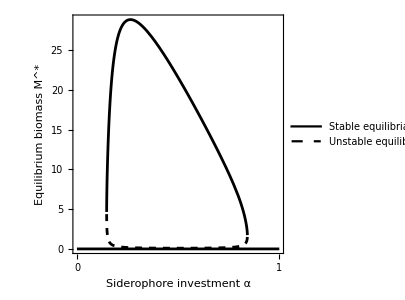

```mathematica
pltvsalpha2=Plot[lines,{α,0,1},
PlotStyle->{Black,{Black,Dashed},Black},
Frame->True,FrameLabel->{"Siderophore investment α","Equilibrium biomass M^*"},
PlotTheme->"Default",BaseStyle->Directive[FontSize->13,FontColor->Black],LabelStyle->Directive[FontSize->11,FontColor->Black],
PlotLegends->Placed[LineLegend[{Black,{Black,Dashed}},{"Stable equilibria", "Unstable equilibrium"},LegendMarkerSize->{22,10}],{Right,Top}],
PlotRange->{-1,All},
PlotRangeClipping->False,
FrameTicks->{{Automatic,None},{{0,1},None}},
ImageSize->300,AspectRatio->1
]
```

### CC tradeoff

Select for the real solution

```mathematica
Mstar[a_]:=
If[a==0, 
Mzero/.defaults,
First@Select[
  Evaluate[M[t] /. (sols /. defaults)/.α->a], 
  Function[Mval, Mval > 0 && NumericQ[Mval] && Im[Mval] == 0]
]];
Mstar[0]
Mstar[0.01]
Mstar[0.1]
```

24.1225

30.9406

120.845

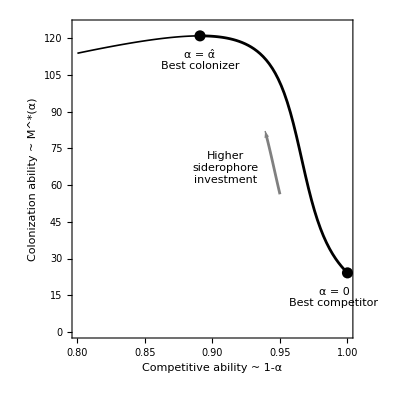

```mathematica
pltCC=Show[ParametricPlot[{1-a,Mstar[a]},{a,0,alphahat}, (* frontier *)
PlotStyle->Black,
PlotRange->{{0.80,1},{0,125}},
Frame->True,FrameLabel->{"Competitive ability ~ 1-α","Colonization ability ~ M^*(α)"},
PlotTheme->"Default",BaseStyle->Directive[FontSize->13,FontColor->Black],
LabelStyle->Directive[FontSize->13,FontColor->Black],AspectRatio->1,
Epilog->{
Directive[PointSize[0.02]],
Point[{1-a,Mstar[a]}/.a->0],
Text["α = 0\nBest competitor",{1-a-0.01,Mstar[a]-10}/.a->0,{1,0}],
Point[{1-a,Mstar[a]}/.a->alphahat],
Text["α = α̂\nBest colonizer",{1-a,Mstar[a]-10}/.a->alphahat],
Directive[Gray],
Arrow[{{1-a-0.02,Mstar[a]-5}/.(a->0.04), {1-a-0.02,Mstar[a]-5}/.(a->0.041)}],
Directive[Black,FontSize->11],
Text["Higher\nsiderophore\ninvestment",{0.91,67}]
},
ImageSize->{300}
],
ParametricPlot[{1-a,Mstar[a]},{a,alphahat,0.2},PlotStyle->{Black,Thickness[0.003]}],
ParametricPlot[{1-a-0.02,Mstar[a]-5},{a,0.03,0.04},PlotStyle->Gray] (* arrow*)
]
```

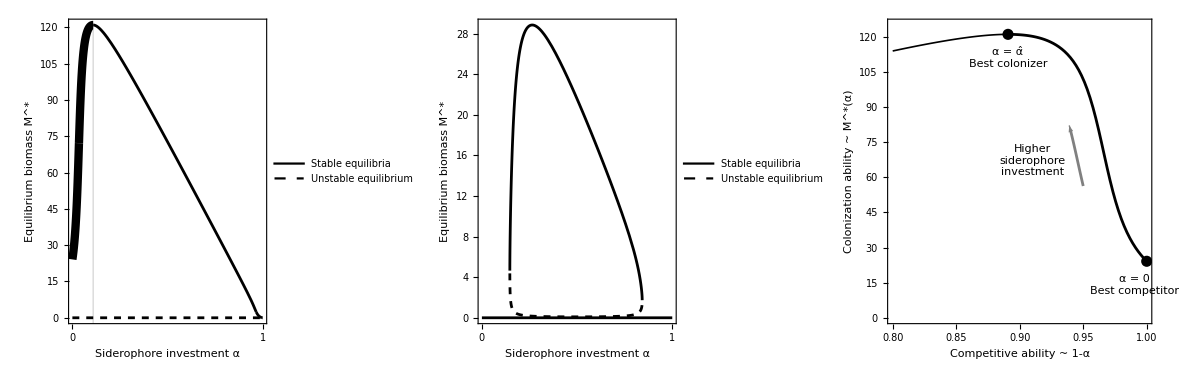

```mathematica
GraphicsRow[{pltvsalpha,pltvsalpha2,pltCC}, ImageSize->Full]
```

## Multiple strains

```mathematica
dr^2 Q==kf (ϵ Sum[α[j] M[j][t],{j,N}]+sApo-Q) (sFe-Q)/.N->2
```

dr^2 Q==kf (-Q+sFe) (-Q+sApo+ϵ (α[1] M[1][t]+α[2] M[2][t]))

```mathematica
Clear[ChelationRate];
Clear[GenerateSidModel]
ChelationRate[N_]:=Module[{ChelationRate},(
ChelationRate=dr^2 Q==kf (ϵ Sum[α[j] M[j][t],{j,N}]+sApo-Q) (sFe-Q);
ChelationRate=Min[SolveValues[ChelationRate,Q]]
)];
GenerateSidModel[N_]:=(
Table[M[i]'[t]== (((1-α[i])γ vh Q)/(vh Sum[M[j][t],{j,N}]+Kh dr)-dm)M[i][t]
,{i,1,N}]/.Q->ChelationRate[N]
);
```

```mathematica
ChelationRate[2]
```

Min[-1/(2 kf)(-dr^2-kf sApo-kf sFe-kf ϵ α[1] M[1][t]-kf ϵ α[2] M[2][t]-√((dr^2+kf sApo+kf sFe+kf ϵ α[1] M[1][t]+kf ϵ α[2] M[2][t])^2+4 kf (-kf sApo sFe-kf sFe ϵ α[1] M[1][t]-kf sFe ϵ α[2] M[2][t]))),-1/(2 kf)(-dr^2-kf sApo-kf sFe-kf ϵ α[1] M[1][t]-kf ϵ α[2] M[2][t]+√((dr^2+kf sApo+kf sFe+kf ϵ α[1] M[1][t]+kf ϵ α[2] M[2][t])^2+4 kf (-kf sApo sFe-kf sFe ϵ α[1] M[1][t]-kf sFe ϵ α[2] M[2][t])))]

```mathematica
GenerateSidModel[1]
```

{M[1]'[t]==M[1][t] (-dm+1/(dr Kh+vh M[1][t])vh γ Min[1/(2 kf)(dr^2+kf sApo+kf sFe+kf ϵ α[1] M[1][t]-√((dr^2+kf sApo+kf sFe+kf ϵ α[1] M[1][t])^2+4 kf (-kf sApo sFe-kf sFe ϵ α[1] M[1][t]))),1/(2 kf)(dr^2+kf sApo+kf sFe+kf ϵ α[1] M[1][t]+√((dr^2+kf sApo+kf sFe+kf ϵ α[1] M[1][t])^2+4 kf (-kf sApo sFe-kf sFe ϵ α[1] M[1][t])))] (1-α[1]))}

```mathematica
Solve[(Map[0==#[[2]]&,GenerateSidModel[1]]/.defaults/.α[1]->alphahat),{M[1][t]},NonNegativeReals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{M[1][t]→0},{M[1][t]→121.012}}

```mathematica
maxbiomass
```

121.012

```mathematica
GenerateSidModel[2]
```

{M[1]'[t]==M[1][t] (-dm+1/(dr Kh+vh (M[1][t]+M[2][t]))vh γ Min[-1/(2 kf)(-dr^2-kf sApo-kf sFe-kf ϵ α[1] M[1][t]-kf ϵ α[2] M[2][t]-√((dr^2+kf sApo+kf sFe+kf ϵ α[1] M[1][t]+kf ϵ α[2] M[2][t])^2+4 kf (-kf sApo sFe-kf sFe ϵ α[1] M[1][t]-kf sFe ϵ α[2] M[2][t]))),-1/(2 kf)(-dr^2-kf sApo-kf sFe-kf ϵ α[1] M[1][t]-kf ϵ α[2] M[2][t]+√((dr^2+kf sApo+kf sFe+kf ϵ α[1] M[1][t]+kf ϵ α[2] M[2][t])^2+4 kf (-kf sApo sFe-kf sFe ϵ α[1] M[1][t]-kf sFe ϵ α[2] M[2][t])))] (1-α[1])),M[2]'[t]==M[2][t] (-dm+1/(dr Kh+vh (M[1][t]+M[2][t]))vh γ Min[-1/(2 kf)(-dr^2-kf sApo-kf sFe-kf ϵ α[1] M[1][t]-kf ϵ α[2] M[2][t]-√((dr^2+kf sApo+kf sFe+kf ϵ α[1] M[1][t]+kf ϵ α[2] M[2][t])^2+4 kf (-kf sApo sFe-kf sFe ϵ α[1] M[1][t]-kf sFe ϵ α[2] M[2][t]))),-1/(2 kf)(-dr^2-kf sApo-kf sFe-kf ϵ α[1] M[1][t]-kf ϵ α[2] M[2][t]+√((dr^2+kf sApo+kf sFe+kf ϵ α[1] M[1][t]+kf ϵ α[2] M[2][t])^2+4 kf (-kf sApo sFe-kf sFe ϵ α[1] M[1][t]-kf sFe ϵ α[2] M[2][t])))] (1-α[2]))}

## Representative Dynamics

```mathematica
Clear[SolvePatch];
SolvePatch[alphas_,start_:1,params_:{},maxT_:1000,stop_:True]:=Module[
{
size=Length[alphas],
starts,
odes,
stateVars,
conditions,
method,
endT=maxT,
sol
},
Clear[M,t,α];
starts=If[NumericQ[start],ConstantArray[start,size],start];
If[size!=Length[starts],Print["Vectors are of unequal size!"];Abort[]];
odes=GenerateSidModel[size];
stateVars=Array[M,size];
conditions=Join[params,defaults];
method=If[stop,
{"EventLocator",
"Event"->Total[Abs[Map[First,odes]]]>10^-6,
"EventAction":>Throw[endT= t,"StopIntegration"]},
Automatic];
sol=NDSolve[{
odes,
Thread[Array[M[#][0]&,size]==starts]
}//.conditions//.Thread[Array[α,size]->alphas],
stateVars,{t,0,maxT},
Method->method
];
Association[Append[sol[[1]],"end"->endT]]
];

Fstar[sol_,alphas_,params_]:=Module[{size=Length[alphas]},
Function[t,Module[{apo},
apo=sApo+ϵ*Sum[alphas[[i]] M[i][t],{i,size}]/.params/. Normal[sol];
fstar=(kf*sFe+apo)+dr^2-Sqrt[(kf*(sFe+apo)+dr^2)^2-4 kf^2 sFe apo ]/.params;
fstar
]]
]
```

```mathematica
Fstarextinction=(kf*sFe+sApo)+dr^2-Sqrt[(kf*(sFe+sApo)+dr^2)^2-4 kf^2 sFe sApo ]/.defaults
```

7-√29

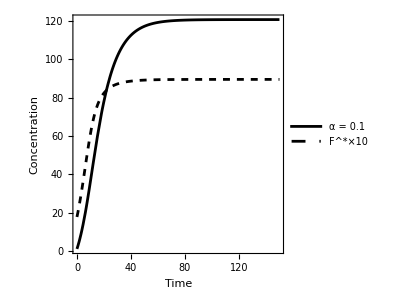

```mathematica
alphas={0.1,0};
sol1=SolvePatch[{0.1,0},{1,0},{},
200,False];

legend={"α = 0.1",Row[{"F^*",Style["×10",11]}]};
Plot[Evaluate[Reverse[{
M[1][t]/.sol1,
10*Fstar[sol1,alphas,defaults][t]
}]],{t,0,Min[sol1["end"],150]},
PlotRange->{0,All},
PlotLegends->Placed[LineLegend[
Reverse[legend],LegendLayout->"ReversedColumn",
LegendMarkerSize->{22,5}],
{0.2,0.8}],
Frame->True,FrameLabel->{"Time","Concentration"},
PlotStyle->{Directive[Black,Dashed],Black},
BaseStyle->Directive[FontSize->14,FontColor->Black],LabelStyle->Directive[FontSize->14,FontColor->Black],
ImageSize->300,AspectRatio->1
]
```

```mathematica
Map[#[150]&,sol1]
```

<|M[1]→120.844,M[2]→0.,end→200[150]|>

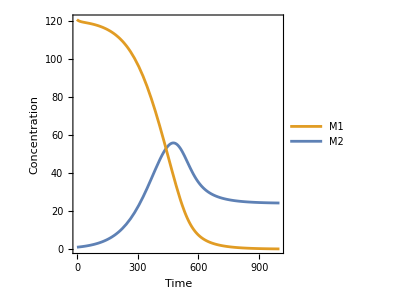

```mathematica
sol2=SolvePatch[{0.1,0},{120.84419770883896,1},{},
2000,False];

legend=Reverse[{"M1","M2"}];
Plot[Evaluate[Reverse[{
M[1][t]/.sol2, 
M[2][t]/.sol2
}]],{t,0,Min[sol2["end"],1000]},
PlotRange->{0,All},
PlotLegends->Placed[LineLegend[
legend,LegendLayout->"ReversedColumn",
LegendMarkerSize->{22,5}],
{0.2,0.8}],
Frame->True,FrameLabel->{"Time","Concentration"},
BaseStyle->Directive[FontSize->14,FontColor->Black],LabelStyle->Directive[FontSize->14,FontColor->Black],
ImageSize->300,AspectRatio->1
]
```

```mathematica
vars={M[2],M[1]};
t0=50;t1=t0+150; tend=t1+1000;
combo[t_]:=Table[Piecewise[{
{None[t],t<t0},
{var[t-t0]/.{M[2]->None}/.sol1,t0<=t<=t1},
{var[t-t1]/.sol2,t1<t<=tend}
}],{var,vars}];
fstarcombo[t_]:=Piecewise[{
{10*Fstarextinction,t<=t0},
{10*Fstar[sol1,alphas,defaults][t-t0],t0<t<=t1},
{10*Fstar[sol2,alphas,defaults][t-t1],t1<t<=tend}
}
]
```

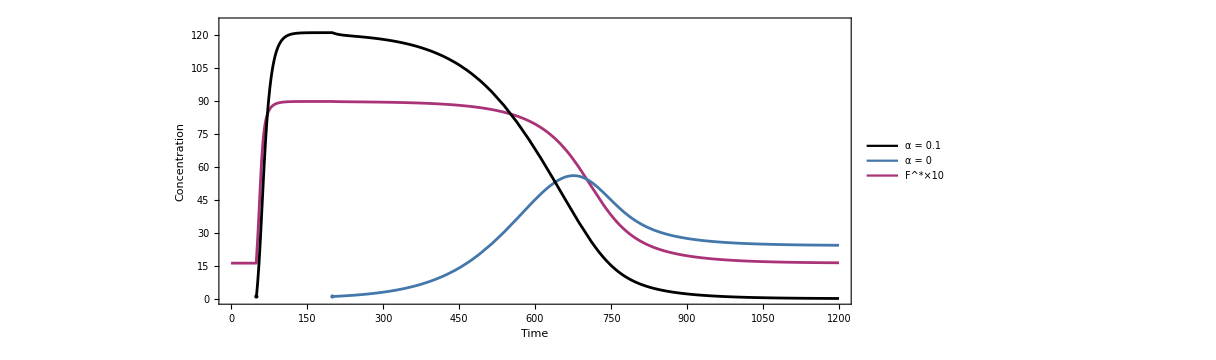

```mathematica
legend={Row[{"F^*",Style["×10",11]}],"α = 0","α = 0.1"};
colors={Black,RGBColor["#4477AA"],RGBColor["#AA3377"]};
pltDyn=Plot[Evaluate[{fstarcombo[t],combo[t]}],{t,0,tend},
PlotRange->{0,125},PlotRangePadding->{{0,-3},{0,0}},

PlotLegends->Placed[LineLegend[
colors,Reverse[legend],LegendMarkerSize->{25,10}],
{0.8,Top}],
Frame->True,FrameLabel->{"Time","Concentration"},FrameTicks->{{Automatic,None},{Automatic,None}},
PlotStyle->Reverse[colors],
BaseStyle->Directive[FontSize->14,FontColor->Black],LabelStyle->Directive[FontSize->13,FontColor->Black],
Prolog->{
(*Opacity[0],EdgeForm[{Gray,Thickness[0.003]}],Rectangle[{t2,0},{tend,0.15}]*)
},
Epilog->{
RGBColor["#4477AA"],PointSize->0.01,
Point[{t1,1}],
Black,PointSize->0.01,
Point[{t0,1}]
},
ImageSize->{900,300},AspectRatio->0.4
]
```